```mathematica
(*  F[1, {0}] = electron neutrino, F[1, {1}] = muon neutrino, F[1, {2}] = tau neutrino, 
	F[2, {0}] = electron, F[2, {1}] = muon, F[2, {2}] = tau,  
	F[3, {0}] = up, F[3, {1}] = charm, F[3, {2}] = top,  
	F[4, {0}] = down, F[4, {1}] = strange, F[4, {2}] = bottom, 
	V[1] = photon, V[2] = Z, V[3] = W-, S[1] = H *)
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
topology = CreateTopologies[0,2->2];
```

FeynCalc 10.0.0 (dev version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

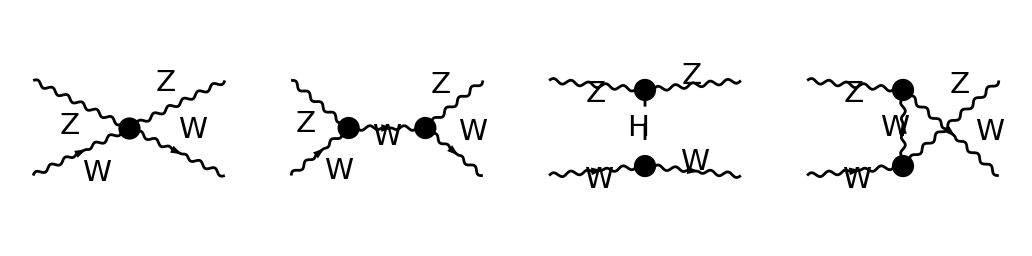

-1/(((OverBar[p_3]+OverBar[p_4])^2-m_W^2) (sin(θ_W))^2)((2 (OverBar[p_3]·(ε̄)^*(p_4))+OverBar[p_4]·(ε̄)^*(p_4)) (-((OverBar[p_2]·(ε̄)^*(p_3)-OverBar[p_1]·(ε̄)^*(p_3)) (ε̄(p_1)·ε̄(p_2)))-(OverBar[p_1]·ε̄(p_2)+OverBar[p_3]·ε̄(p_2)+OverBar[p_4]·ε̄(p_2)) (ε̄(p_1)·(ε̄)^*(p_3))-(-(OverBar[p_2]·ε̄(p_1))-OverBar[p_3]·ε̄(p_1)-OverBar[p_4]·ε̄(p_1)) (ε̄(p_2)·(ε̄)^*(p_3)))+(OverBar[p_3]·(ε̄)^*(p_3)+2 (OverBar[p_4]·(ε̄)^*(p_3))) ((OverBar[p_2]·(ε̄)^*(p_4)-OverBar[p_1]·(ε̄)^*(p_4)) (ε̄(p_1)·ε̄(p_2))+(OverBar[p_1]·ε̄(p_2)+OverBar[p_3]·ε̄(p_2)+OverBar[p_4]·ε̄(p_2)) (ε̄(p_1)·(ε̄)^*(p_4))+(-(OverBar[p_2]·ε̄(p_1))-OverBar[p_3]·ε̄(p_1)-OverBar[p_4]·ε̄(p_1)) (ε̄(p_2)·(ε̄)^*(p_4)))+(OverBar[p_1]·ε̄(p_2)) (OverBar[p_3]·ε̄(p_1)-OverBar[p_4]·ε̄(p_1)) ((ε̄)^*(p_3)·(ε̄)^*(p_4))+(OverBar[p_3]·ε̄(p_2)) (OverBar[p_3]·ε̄(p_1)-OverBar[p_4]·ε̄(p_1)) ((ε̄)^*(p_3)·(ε̄)^*(p_4))-(OverBar[p_2]·ε̄(p_1)) (OverBar[p_3]·ε̄(p_2)-OverBar[p_4]·ε̄(p_2)) ((ε̄)^*(p_3)·(ε̄)^*(p_4))-(OverBar[p_3]·ε̄(p_1)) (OverBar[p_3]·ε̄(p_2)-OverBar[p_4]·ε̄(p_2)) ((ε̄)^*(p_3)·(ε̄)^*(p_4))-(OverBar[p_4]·ε̄(p_1)) (OverBar[p_3]·ε̄(p_2)-OverBar[p_4]·ε̄(p_2)) ((ε̄)^*(p_3)·(ε̄)^*(p_4))+(OverBar[p_3]·ε̄(p_1)-OverBar[p_4]·ε̄(p_1)) (OverBar[p_4]·ε̄(p_2)) ((ε̄)^*(p_3)·(ε̄)^*(p_4))+(-(OverBar[p_1]·OverBar[p_3])+OverBar[p_1]·OverBar[p_4]+OverBar[p_2]·OverBar[p_3]-OverBar[p_2]·OverBar[p_4]) (ε̄(p_1)·ε̄(p_2)) ((ε̄)^*(p_3)·(ε̄)^*(p_4))) (cos(θ_W))^2 e^2+1/(((OverBar[p_3]-OverBar[p_2])^2-m_W^2) (sin(θ_W))^2)((OverBar[p_1]·(ε̄)^*(p_4)) (-(OverBar[p_2]·ε̄(p_1))-OverBar[p_3]·ε̄(p_1)) (ε̄(p_2)·(ε̄)^*(p_3))-(OverBar[p_2]·(ε̄)^*(p_4)) (-(OverBar[p_2]·ε̄(p_1))-OverBar[p_3]·ε̄(p_1)) (ε̄(p_2)·(ε̄)^*(p_3))+(OverBar[p_2]·ε̄(p_1)) (-(OverBar[p_2]·(ε̄)^*(p_4))-OverBar[p_3]·(ε̄)^*(p_4)) (ε̄(p_2)·(ε̄)^*(p_3))-(OverBar[p_3]·ε̄(p_1)) (-(OverBar[p_2]·(ε̄)^*(p_4))-OverBar[p_3]·(ε̄)^*(p_4)) (ε̄(p_2)·(ε̄)^*(p_3))+(-(OverBar[p_2]·ε̄(p_1))-OverBar[p_3]·ε̄(p_1)) (OverBar[p_3]·(ε̄)^*(p_4)) (ε̄(p_2)·(ε̄)^*(p_3))+(-(OverBar[p_2]·(ε̄)^*(p_4))-OverBar[p_3]·(ε̄)^*(p_4)) (OverBar[p_4]·ε̄(p_1)) (ε̄(p_2)·(ε̄)^*(p_3))+(OverBar[p_1]·OverBar[p_2]+OverBar[p_1]·OverBar[p_3]+OverBar[p_2]·OverBar[p_4]+OverBar[p_3]·OverBar[p_4]) (ε̄(p_1)·(ε̄)^*(p_4)) (ε̄(p_2)·(ε̄)^*(p_3))+(2 (OverBar[p_2]·(ε̄)^*(p_3))-OverBar[p_3]·(ε̄)^*(p_3)) ((OverBar[p_1]·(ε̄)^*(p_4)-OverBar[p_2]·(ε̄)^*(p_4)+OverBar[p_3]·(ε̄)^*(p_4)) (ε̄(p_1)·ε̄(p_2))+(-(OverBar[p_1]·ε̄(p_2))-OverBar[p_4]·ε̄(p_2)) (ε̄(p_1)·(ε̄)^*(p_4))+(OverBar[p_2]·ε̄(p_1)-OverBar[p_3]·ε̄(p_1)+OverBar[p_4]·ε̄(p_1)) (ε̄(p_2)·(ε̄)^*(p_4)))+(OverBar[p_2]·ε̄(p_2)-2 (OverBar[p_3]·ε̄(p_2))) (-((OverBar[p_1]·(ε̄)^*(p_4)-OverBar[p_2]·(ε̄)^*(p_4)+OverBar[p_3]·(ε̄)^*(p_4)) (ε̄(p_1)·(ε̄)^*(p_3)))-(-(OverBar[p_1]·(ε̄)^*(p_3))-OverBar[p_4]·(ε̄)^*(p_3)) (ε̄(p_1)·(ε̄)^*(p_4))-(OverBar[p_2]·ε̄(p_1)-OverBar[p_3]·ε̄(p_1)+OverBar[p_4]·ε̄(p_1)) ((ε̄)^*(p_3)·(ε̄)^*(p_4)))) (cos(θ_W))^2 e^2-((ε̄(p_1)·(ε̄)^*(p_3)) (ε̄(p_2)·(ε̄)^*(p_4)) e^2 m_W^2)/(((OverBar[p_4]-OverBar[p_2])^2-m_H^2) (cos(θ_W))^2 (sin(θ_W))^2)-ⅈ ((ⅈ (ε̄(p_1)·(ε̄)^*(p_4)) (ε̄(p_2)·(ε̄)^*(p_3)) (cos(θ_W))^2 e^2)/(sin(θ_W))^2-(2 ⅈ (ε̄(p_1)·(ε̄)^*(p_3)) (ε̄(p_2)·(ε̄)^*(p_4)) (cos(θ_W))^2 e^2)/(sin(θ_W))^2+(ⅈ (ε̄(p_1)·ε̄(p_2)) ((ε̄)^*(p_3)·(ε̄)^*(p_4)) (cos(θ_W))^2 e^2)/(sin(θ_W))^2)

1/(144 (cos(θ_W))^4 m_W^4 m_Z^4 (sin(θ_W))^4)e^4 ((4 m_W^8-176 m_Z^2 m_W^6-8 s m_W^6+40 t m_W^6-8 u m_W^6+152 m_Z^4 m_W^4+8 s^2 m_W^4+16 t^2 m_W^4+8 u^2 m_W^4+168 s m_Z^2 m_W^4+24 t m_Z^2 m_W^4+168 u m_Z^2 m_W^4-40 s t m_W^4+8 s u m_W^4-40 t u m_W^4-176 m_Z^6 m_W^2+168 s m_Z^4 m_W^2+24 t m_Z^4 m_W^2+168 u m_Z^4 m_W^2-4 s^3 m_W^2-16 t^3 m_W^2-4 u^3 m_W^2+8 s t^2 m_W^2-4 s u^2 m_W^2+8 t u^2 m_W^2-32 s^2 m_Z^2 m_W^2+48 t^2 m_Z^2 m_W^2-32 u^2 m_Z^2 m_W^2-80 s t m_Z^2 m_W^2-80 s u m_Z^2 m_W^2-80 t u m_Z^2 m_W^2+8 s^2 t m_W^2-4 s^2 u m_W^2+8 t^2 u m_W^2+24 s t u m_W^2+4 m_Z^8-8 s m_Z^6+40 t m_Z^6-8 u m_Z^6+s^4+4 t^4+u^4+8 s^2 m_Z^4+16 t^2 m_Z^4+8 u^2 m_Z^4-40 s t m_Z^4+8 s u m_Z^4-40 t u m_Z^4-4 s^2 t^2+2 s^2 u^2-4 t^2 u^2-4 s^3 m_Z^2-16 t^3 m_Z^2-4 u^3 m_Z^2+8 s t^2 m_Z^2-4 s u^2 m_Z^2+8 t u^2 m_Z^2+8 s^2 t m_Z^2-4 s^2 u m_Z^2+8 t^2 u m_Z^2+24 s t u m_Z^2+1/((OverBar[p_3]+OverBar[p_4])^2-m_W^2)2 (-2 (88 m_Z^2+s-12 t) m_W^8+(-976 m_Z^4+8 (35 s+13 t+23 u) m_Z^2+5 s^2+t^2+3 u^2-56 s t-12 t u) m_W^6-(976 m_Z^6-4 (149 s+72 t+108 u) m_Z^4+(77 s^2+8 (19 t+40 u) s-5 (3 t^2-12 u t+u^2)) m_Z^2+3 s^3+6 t^3+4 u^3-7 t u^2-7 t^2 u+s^2 (4 u-33 t)+s (3 t^2-24 u t+u^2)) m_W^4+(-176 m_Z^8+8 (35 s+13 t+23 u) m_Z^6-(77 s^2+8 (19 t+40 u) s-5 (3 t^2-12 u t+u^2)) m_Z^4+2 (3 s^3+(19 t+30 u) s^2+(-5 t^2+48 u t+21 u^2) s-8 t^3-6 u^3+5 t u^2+5 t^2 u) m_Z^2+2 t^4+u^4-3 t^2 u^2-s^3 (t-4 u)-s^2 (5 t^2+12 u t+u^2)+s (8 t^3-5 u t^2-7 u^2 t+4 u^3)) m_W^2-2 (s-12 t) m_Z^8+(5 s^2-56 t s+t^2+3 u^2-12 t u) m_Z^6-(3 s^3+(4 u-33 t) s^2+(3 t^2-24 u t+u^2) s+6 t^3+4 u^3-7 t u^2-7 t^2 u) m_Z^4-(-2 t^4+3 u^2 t^2-u^4+s^3 (t-4 u)+s^2 (5 t^2+12 u t+u^2)+s (-8 t^3+5 u t^2+7 u^2 t-4 u^3)) m_Z^2+s (t^2-u^2) (s^2-2 t^2+u^2))+(1/((OverBar[p_3]-OverBar[p_2])^2-m_W^2))^2 (-20 m_W^12+2 (-116 m_Z^2+7 s+7 t+33 u) m_W^10+(1172 m_Z^4-2 (65 s+65 t-417 u) m_Z^2+11 s^2+3 t^2-70 u^2-68 t u-6 s (t+10 u)) m_W^8+(3792 m_Z^6-4 (227 s+227 t-367 u) m_Z^4+4 (31 s^2-22 t s-28 u s+15 t^2-194 u^2-12 t u) m_Z^2-4 s^3-4 t^3+23 u^3+92 t u^2+s^2 (4 t-19 u)-3 t^2 u+s (4 t^2+26 u t+76 u^2)) m_W^6+(1172 m_Z^8-4 (227 s+227 t-367 u) m_Z^6+2 (113 s^2-82 t s+12 u s+185 t^2-738 u^2-44 t u) m_Z^4+(-44 s^3+(44 t-97 u) s^2+(44 t^2+62 u t+316 u^2) s-44 t^3+165 u^3+300 t u^2-113 t^2 u) m_Z^2+s^4+8 s^3 u+s^2 (-2 t^2-8 u t+5 u^2)-2 s u (4 t^2+17 u t+14 u^2)+t (t^3+8 u t^2-3 u^2 t-36 u^3)) m_W^4+(-232 m_Z^10-2 (65 s+65 t-417 u) m_Z^8+4 (31 s^2-22 t s-28 u s+15 t^2-194 u^2-12 t u) m_Z^6+(-44 s^3+(44 t-97 u) s^2+(44 t^2+62 u t+316 u^2) s-44 t^3+165 u^3+300 t u^2-113 t^2 u) m_Z^4+2 (5 s^4+8 u s^3+(-10 t^2-8 u t+u^2) s^2-2 u (4 t^2+21 u t+18 u^2) s+t (5 t^3+8 u t^2+9 u^2 t-28 u^3)) m_Z^2+u (-2 s^4-4 u s^3+(4 t^2+4 u t+3 u^2) s^2-2 u (-2 t^2-7 u t+u^2) s-2 t^4+u^4-2 t u^3+3 t^2 u^2-4 t^3 u)) m_W^2+(u-m_Z^2)^2 (-20 m_Z^8+2 (7 s+7 t+13 u) m_Z^6+(11 s^2-6 t s-32 u s+3 t^2+2 u^2-40 t u) m_Z^4+(-4 s^3+(4 t+3 u) s^2+2 (2 t^2+7 u t-u^2) s-4 t^3+u^3-2 t u^2+3 t^2 u) m_Z^2+(s^2-t^2)^2))+(1/((OverBar[p_3]+OverBar[p_4])^2-m_W^2))^2 (-20 m_W^12+2 (-116 m_Z^2+33 s+7 (t+u)) m_W^10-(-1172 m_Z^4+(130 (t+u)-834 s) m_Z^2+70 s^2-3 t^2-11 u^2+68 s t+60 s u+6 t u) m_W^8+(3792 m_Z^6+4 (367 s-227 (t+u)) m_Z^4-4 (194 s^2+4 (3 t+7 u) s-15 t^2-31 u^2+22 t u) m_Z^2+23 s^3-4 (t-u)^2 (t+u)+s^2 (92 t+76 u)+s (-3 t^2+26 u t-19 u^2)) m_W^6+(1172 m_Z^8+4 (367 s-227 (t+u)) m_Z^6-2 (738 s^2+44 t s-12 u s-185 t^2-113 u^2+82 t u) m_Z^4+(165 s^3+4 (75 t+79 u) s^2+(-113 t^2+62 u t-97 u^2) s-44 (t-u)^2 (t+u)) m_Z^2+(t^2-u^2)^2+8 s (t-u)^2 (t+u)-4 s^3 (9 t+7 u)+s^2 (-3 t^2-34 u t+5 u^2)) m_W^4+(-232 m_Z^10+2 (417 s-65 (t+u)) m_Z^8-4 (194 s^2+4 (3 t+7 u) s-15 t^2-31 u^2+22 t u) m_Z^6+(165 s^3+4 (75 t+79 u) s^2+(-113 t^2+62 u t-97 u^2) s-44 (t-u)^2 (t+u)) m_Z^4-2 (4 (7 t+9 u) s^3-(9 t^2-42 u t+u^2) s^2-8 (t-u)^2 (t+u) s-5 (t^2-u^2)^2) m_Z^2+s (s^4-2 (t+u) s^3+(3 t^2+14 u t+3 u^2) s^2-4 (t-u)^2 (t+u) s-2 (t^2-u^2)^2)) m_W^2+(s-m_Z^2)^2 (-20 m_Z^8+2 (13 s+7 (t+u)) m_Z^6+(2 s^2-8 (5 t+4 u) s+3 t^2+11 u^2-6 t u) m_Z^4+(s^3-2 (t+u) s^2+(3 t^2+14 u t+3 u^2) s-4 (t-u)^2 (t+u)) m_Z^2+(t^2-u^2)^2))-1/((OverBar[p_3]-OverBar[p_2])^2-m_W^2)(2 (2 (88 m_Z^2-12 t+u) m_W^8-(-976 m_Z^4+8 (23 s+13 t+35 u) m_Z^2+3 s^2+t^2+5 u^2-12 s t-56 t u) m_W^6+(976 m_Z^6-4 (108 s+72 t+149 u) m_Z^4+(-5 s^2+60 t s+320 u s-15 t^2+77 u^2+152 t u) m_Z^2+4 s^3+s^2 (u-7 t)+s (-7 t^2-24 u t+4 u^2)+3 (2 t^3+u t^2-11 u^2 t+u^3)) m_W^4-(-176 m_Z^8+8 (23 s+13 t+35 u) m_Z^6+(5 s^2-20 (3 t+16 u) s+15 t^2-77 u^2-152 t u) m_Z^4+2 (-6 s^3+(5 t+21 u) s^2+(5 t^2+48 u t+30 u^2) s-8 t^3+3 u^3+19 t u^2-5 t^2 u) m_Z^2+s^4+4 s^3 u-s^2 (3 t^2+7 u t+u^2)+s u (-5 t^2-12 u t+4 u^2)+t (2 t^3+8 u t^2-5 u^2 t-u^3)) m_W^2+(2 u-24 t) m_Z^8-(3 s^2-12 t s+t^2+5 u^2-56 t u) m_Z^6+(4 s^3+(u-7 t) s^2+(-7 t^2-24 u t+4 u^2) s+3 (2 t^3+u t^2-11 u^2 t+u^3)) m_Z^4+(-s^4-4 u s^3+(3 t^2+7 u t+u^2) s^2+u (5 t^2+12 u t-4 u^2) s+t (-2 t^3-8 u t^2+5 u^2 t+u^3)) m_Z^2+(s^2-t^2) u (s^2-2 t^2+u^2))+1/((OverBar[p_3]+OverBar[p_4])^2-m_W^2)(-32 m_W^12+8 (-69 m_Z^2+8 s-6 t+8 u) m_W^10+(-3320 m_Z^4+8 (70 s+9 t+70 u) m_Z^2-24 s^2+6 t^2-24 u^2+58 s t-146 s u+58 t u) m_W^8-2 (3112 m_Z^6-8 (37 s+239 t+37 u) m_Z^4-2 (46 s^2+3 (t-70 u) s-111 t^2+46 u^2+3 t u) m_Z^2+3 s^3-6 t^3+3 u^3+12 t u^2+s^2 (12 t-37 u)+7 t^2 u+s (7 t^2+26 u t-37 u^2)) m_W^6-(1040 m_Z^8+16 (48 s-185 t+48 u) m_Z^6+4 (-239 s^2+66 t s+173 u s+327 t^2-239 u^2+66 t u) m_Z^4+(55 s^3+(181 t+45 u) s^2-5 (19 t^2+30 u t-9 u^2) s-165 t^3+55 u^3+181 t u^2-95 t^2 u) m_Z^2+2 (s^4-(4 t+3 u) s^3+(-6 t^2-7 u t+26 u^2) s^2+(3 t^3-u t^2-7 u^2 t-3 u^3) s+2 t^4+u^4-4 t u^3-6 t^2 u^2+3 t^3 u)) m_W^4+(376 m_Z^10-48 (13 s+10 t+13 u) m_Z^8+4 (152 s^2+93 t s+66 u s-71 t^2+152 u^2+93 t u) m_Z^6-2 (44 s^3+(105 t+134 u) s^2-2 (17 t^2+6 u t-67 u^2) s-59 t^3+44 u^3+105 t u^2-34 t^2 u) m_Z^4+(-19 s^4+(33 t+60 u) s^3+(19 t^2+55 u t+14 u^2) s^2+(-45 t^3-26 u t^2+55 u^2 t+60 u^3) s-4 t^4-19 u^4+33 t u^3+19 t^2 u^2-45 t^3 u) m_Z^2+2 (u s^4+(-t^2-3 u t+u^2) s^3+(u^3-3 t^2 u) s^2+(t^4+4 u t^3-3 u^2 t^2-3 u^3 t+u^4) s+t^2 u (t^2-u^2))) m_W^2+40 m_Z^12-8 (10 s+7 t+10 u) m_Z^10+2 (34 s^2+39 t s+51 u s-9 t^2+34 u^2+39 t u) m_Z^8-(27 s^3+(41 t+49 u) s^2+(-11 t^2+90 u t+49 u^2) s-17 t^3+27 u^3+41 t u^2-11 t^2 u) m_Z^6-(s^4-13 (t+2 u) s^3+(-11 t^2-37 u t+22 u^2) s^2+(11 t^3+24 u t^2-37 u^2 t-26 u^3) s+4 t^4+u^4-13 t u^3-11 t^2 u^2+11 t^3 u) m_Z^4+(u s^4+(-2 t^2-11 u t+3 u^2) s^3+u (-5 t^2-6 u t+3 u^2) s^2+(2 t^4+13 u t^3-5 u^2 t^2-11 u^3 t+u^4) s+2 t^2 u (t^2-u^2)) m_Z^2+2 s (s^2-t^2) u (t^2-u^2)))) (cos(θ_W))^8+1/((OverBar[p_4]-OverBar[p_2])^2-m_H^2)2 (cos(θ_W))^4 m_W^2 (-72 m_Z^2 m_W^6+12 t m_W^6+80 m_Z^4 m_W^4+14 t^2 m_W^4+72 s m_Z^2 m_W^4-28 t m_Z^2 m_W^4+72 u m_Z^2 m_W^4-12 s t m_W^4-12 t u m_W^4-72 m_Z^6 m_W^2+72 s m_Z^4 m_W^2-28 t m_Z^4 m_W^2+72 u m_Z^4 m_W^2-8 t^3 m_W^2+2 s t^2 m_W^2+2 t u^2 m_W^2-20 s^2 m_Z^2 m_W^2+28 t^2 m_Z^2 m_W^2-20 u^2 m_Z^2 m_W^2-24 s t m_Z^2 m_W^2-32 s u m_Z^2 m_W^2-24 t u m_Z^2 m_W^2+2 s^2 t m_W^2+2 t^2 u m_W^2+8 s t u m_W^2+12 t m_Z^6+2 t^4+14 t^2 m_Z^4-12 s t m_Z^4-12 t u m_Z^4-s^2 t^2-t^2 u^2-8 t^3 m_Z^2+2 s t^2 m_Z^2+2 t u^2 m_Z^2+2 s^2 t m_Z^2+2 t^2 u m_Z^2+8 s t u m_Z^2+1/((OverBar[p_3]+OverBar[p_4])^2-m_W^2)(8 (t-6 m_Z^2) m_W^8+(-336 m_Z^4+4 (24 s+11 t+9 u) m_Z^2-22 s t) m_W^6+(-336 m_Z^6+8 (24 s+29 t+5 u) m_Z^4-2 (12 s^2+23 t s+54 u s+2 t^2-6 u^2+12 t u) m_Z^2+t (13 s^2-4 t s+4 u s-2 t^2+3 u^2+3 t u)) m_W^4+(-48 m_Z^8+4 (24 s+11 t+9 u) m_Z^6-2 (12 s^2+23 t s+54 u s+2 t^2-6 u^2+12 t u) m_Z^4+2 (-4 t^3+u t^2+u^2 t-2 u^3+s^2 (3 t+10 u)-2 s (t^2-10 u t-5 u^2)) m_Z^2+t (s^3-2 (t+2 u) s^2+(4 t^2-u t-3 u^2) s+t^3-t u^2)) m_W^2+t (8 m_Z^8-22 s m_Z^6+(13 s^2-4 t s+4 u s-2 t^2+3 u^2+3 t u) m_Z^4+(s^3-2 (t+2 u) s^2+(4 t^2-u t-3 u^2) s+t^3-t u^2) m_Z^2+s t (u^2-t^2)))+1/((OverBar[p_3]-OverBar[p_2])^2-m_W^2)(8 (t-6 m_Z^2) m_W^8+(-336 m_Z^4+4 (9 s+11 t+24 u) m_Z^2-22 t u) m_W^6+(-336 m_Z^6+8 (5 s+29 t+24 u) m_Z^4+2 (6 s^2-6 (2 t+9 u) s-2 t^2-12 u^2-23 t u) m_Z^2+t (3 s^2+3 t s+4 u s-2 t^2+13 u^2-4 t u)) m_W^4+(-48 m_Z^8+4 (9 s+11 t+24 u) m_Z^6+2 (6 s^2-6 (2 t+9 u) s-2 t^2-12 u^2-23 t u) m_Z^4+(-4 s^3+2 (t+10 u) s^2+2 (t^2+20 u t+10 u^2) s-2 t (4 t^2+2 u t-3 u^2)) m_Z^2+t (t^3+4 u t^2-2 u^2 t+u^3-s^2 (t+3 u)-s u (t+4 u))) m_W^2+t (8 m_Z^8-22 u m_Z^6+(3 s^2+3 t s+4 u s-2 t^2+13 u^2-4 t u) m_Z^4+(t^3+4 u t^2-2 u^2 t+u^3-s^2 (t+3 u)-s u (t+4 u)) m_Z^2+t (s^2-t^2) u)))+(1/((OverBar[p_4]-OverBar[p_2])^2-m_H^2))^2 m_W^4 (12 m_W^4-4 t m_W^2+t^2) (12 m_Z^4-4 t m_Z^2+t^2))

```mathematica
(* unpolarised SM: W- Z -> W- Z *)
feynman=InsertFields[topology, {V[2], V[3]}->{V[2], V[3]}, InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p1, p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_Z"],SMP["m_W"],SMP["m_Z"],SMP["m_W"]];
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//DoPolarizationSums[#,p1, ExtraFactor->1/3]&//DoPolarizationSums[#,p2, ExtraFactor->1/3] &//DoPolarizationSums[#,p3]&//DoPolarizationSums[#,p4] &//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude *)
```

```mathematica
Print["\tCPU Time used: ",Round[N[TimeUsed[],4],0.001]," s."];
```

CPU Time used: 76.831 s.

```mathematica
FeynCalcHowToCite[]
```

• V. Shtabovenko, R. Mertig and F. Orellana, arXiv:2312.14089.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

Null